```mathematica
oil=Reverse@{107.457,114.28,116.193,112.928,109.465,106.648,111.571,118.353,124.109,136.339,143.528,148.031,160.898,171.895,185.096,188.745,192.77,197.474,193.817,181.194,181.181,189.364,187.517,167.896,155.807,137.835,129.012,113.464,99.601,90.934,69.616,61.131,52.677,47.802,43.799,38.366,30.857,29.701,30.709,23.65,20.665,16.645,16.227,10.995,2.014,1.87,1.927,0.357}
```

{0.357,1.927,1.87,2.014,10.995,16.227,16.645,20.665,23.65,30.709,29.701,30.857,38.366,43.799,47.802,52.677,61.131,69.616,90.934,99.601,113.464,129.012,137.835,155.807,167.896,187.517,189.364,181.181,181.194,193.817,197.474,192.77,188.745,185.096,171.895,160.898,148.031,143.528,136.339,124.109,118.353,111.571,106.648,109.465,112.928,116.193,114.28,107.457}

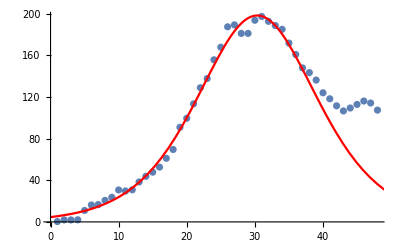

```mathematica
Show[ListPlot@oil,Plot[396.7498145641246/(1+Cosh[0.16920540927553132 (-30.344134070074293+t)]),{t,0,50},PlotStyle->Red]]
```

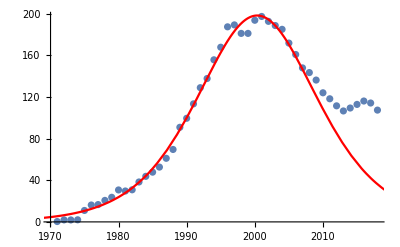

```mathematica
Show[ListPlot@Transpose[{Range[1971,2018],oil}],Plot[396.7498145641246/(1+Cosh[0.16920540927553132 (-30.344134070074293+t-1970)]),{t,1960,2030},PlotStyle->Red]]
```

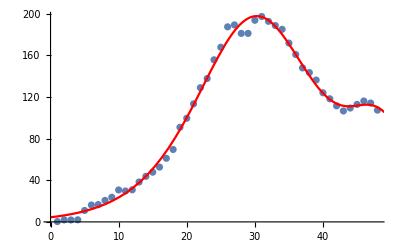

```mathematica
Show[ListPlot@oil,Plot[154.31629428910412/(1+Cosh[0.3006583273558879 (-48.540163515840476+t)])+393.13224985417185/(1+Cosh[0.17134196419990885 (-30.13052674214306+t)]),{t,0,50},PlotStyle->Red]]
```

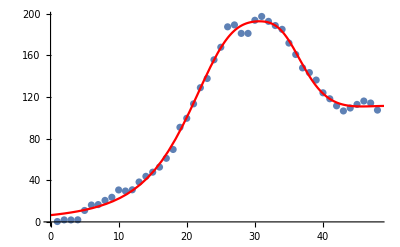

```mathematica
Show[ListPlot@oil,Plot[218.22430942868903/(1+Cosh[0.08458052604931322 (-51.513908786817716+t)])+88.08313705166715/(1+Cosh[0.42003137311129607 (-34.138205491616276+t)])+265.2484436381942/(1+Cosh[0.23103306251304226 (-26.99000150179917+t)]),{t,0,50},PlotStyle->Red]]
```

```mathematica
Length@oil
```

48

```mathematica
oildiff07=oil-Table[396.7498145641246/(1+Cosh[0.16920540927553132 (-30.344134070074293+t)]),{t,1,48}];
```

```mathematica
oildiff12=oil-Table[394.9879969940485/(1+Cosh[0.16011035533611684 (-30.86278019250874+t)]),{t,1,48}];
oildiff18=oil-Table[382.37770683678485/(1+Cosh[0.13924598074210312 (-31.98879766077117+t)]),{t,1,48}];

oildiff18b=oil-Table[393.13224985417185/(1+Cosh[0.17134196419990885 (-30.13052674214306+t)]),{t,1,48}];
```

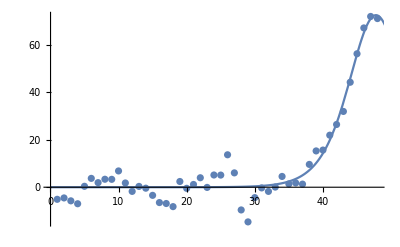

```mathematica
Show[ListPlot[oildiff07,PlotRange->All],Plot[145.2807152467277/(1+Cosh[0.3729293777269684 (-47.78163797735676+t)]),{t,0,50},PlotRange->All]]
```

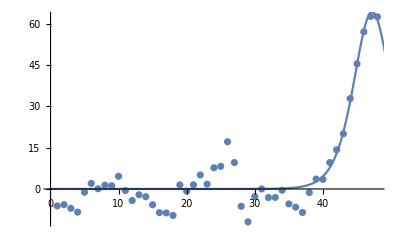

```mathematica
Show[ListPlot[oildiff12,PlotRange->All],Plot[128.73925849659196/(1+Cosh[0.5530795471166822 (-47.216754213320606+t)]),{t,0,50},PlotRange->All]]
```

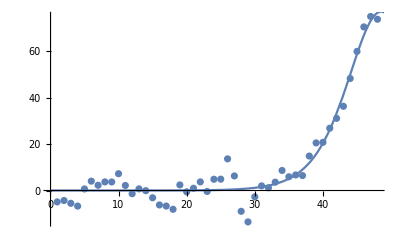

```mathematica
Show[ListPlot[oildiff18b,PlotRange->All],Plot[154.31629428910412/(1+Cosh[0.3006583273558879 (-48.540163515840476+t)]),{t,0,50},PlotRange->All]]
```

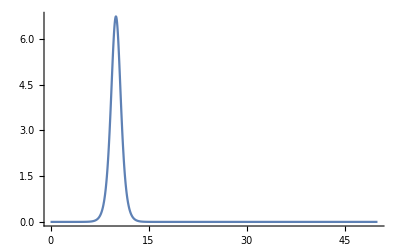

```mathematica
Plot[13.457285566235782/(1+Cosh[2.002780868226367 (-10.+t)]),{t,0,50},PlotRange->All]
```

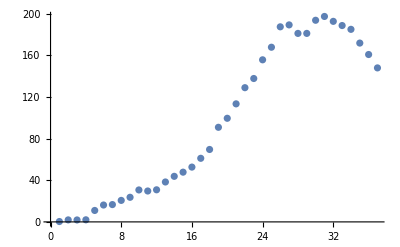

```mathematica
ListPlot@oil[[;;37]]
```

```mathematica
NonlinearModelFit[oil[[;;37]],a/(1+Cosh[b(t-t0)]),{a,b,t0},t]
```

FittedModel[396.75/(1+Cosh[0.169205 (-30.3441+t)])]

```mathematica
NonlinearModelFit[oil[[;;42]],a/(1+Cosh[b(t-t0)]),{a,b,t0},t]
```

FittedModel[394.988/(1+Cosh[0.16011 (-30.8628+t)])]

```mathematica
NonlinearModelFit[oil[[;;]],a/(1+Cosh[b(t-t0)]),{a,b,t0},t]
```

FittedModel[382.378/(1+Cosh[0.139246 (-31.9888+t)])]

```mathematica
NonlinearModelFit[oil[[;;42]],a/(1+Cosh[b(t-t0)])+aa/(1+Cosh[bb(t-t1)]),{a,b,t0,aa,bb,t1},t]
```

FittedModel[356.246/(1+Cosh[0.15253 (-32.0026+t)])+66.5686/(1+Cosh[0.357637 (-25.5368+t)])]

```mathematica
NonlinearModelFit[oil[[;;]],a/(1+Cosh[b(t-t0)])+aa/(1+Cosh[bb(t-t1)]),{a,b,t0,aa,bb,t1},t,AccuracyGoal->7]
```

FittedModel[154.316/(1+Cosh[0.300658 (-48.5402+t)])+393.132/(1+Cosh[0.171342 (-30.1305+t)])]

```mathematica
NonlinearModelFit[oil[[;;]],a/(1+Cosh[b(t-t0)])+aa/(1+Cosh[bb(t-t1)])+aaa/(1+Cosh[bbb(t-t2)]),{a,b,t0,aa,bb,t1,aaa,bbb,t2},t,AccuracyGoal->8]["BestFit"]
```

218.224/(1+Cosh[0.0845805 (-51.5139+t)])+88.0831/(1+Cosh[0.420031 (-34.1382+t)])+265.248/(1+Cosh[0.231033 (-26.99+t)])

```mathematica
NonlinearModelFit[oil[[;;31]],a/(1+Cosh[b(t-t0)]),{a,b,t0,aa,bb,t1},t]
```

FittedModel[387.937/(1+Cosh[0.179297 (-29.5141+t)])]

```mathematica
NonlinearModelFit[oil[[;;]],
{393.13224985417185/(1+Cosh[0.17134196419990885 (-30.13052674214306+t)])+aa/(1+Cosh[bb(t-t1)]),aa>0&&0<bb<1&&t1>0},
{aa,bb,t1},t]
```

FittedModel[393.132/(1+Cosh[0.171342 (-30.1305+t)])+10.8492/(1+Cosh[1. (-9.20112+t)])]

```mathematica
NonlinearModelFit[oildiff12[[;;]],{a/(1+Cosh[b(t-t0)]),a>0&&b>0&&40<t0},{a,b,t0},t]
```

FittedModel[128.739/(1+Cosh[0.55308 (-47.2168+t)])]

```mathematica
%112["BestFit"]
```

382.378/(1+Cosh[0.139246 (-31.9888+t)])

```mathematica
%103["Response"]
```

{107.457,114.28,116.193,112.928,109.465,106.648,111.571,118.353,124.109,136.339,143.528,148.031,160.898,171.895,185.096,188.745,192.77,197.474,193.817,181.194,181.181,189.364,187.517,167.896,155.807,137.835,129.012,113.464,99.601,90.934,69.616,61.131,52.677,47.802,43.799,38.366,30.857,29.701,30.709,23.65,20.665,16.645,16.227,10.995,2.014,1.87,1.927,0.357}

```mathematica
%103["Function"]
```

382.378/(1+Cosh[0.139246 (-17.0112+#1)])&

```mathematica
List@@%
```

{{Nonlinear,{a→382.378,b→-0.139246,t0→17.0112},{{t},a/(1+Cosh[b (t-t0)])}},{1},{107.457,114.28,116.193,112.928,109.465,106.648,111.571,118.353,124.109,136.339,143.528,148.031,160.898,171.895,185.096,188.745,192.77,197.474,193.817,181.194,181.181,189.364,187.517,167.896,155.807,137.835,129.012,113.464,99.601,90.934,69.616,61.131,52.677,47.802,43.799,38.366,30.857,29.701,30.709,23.65,20.665,16.645,16.227,10.995,2.014,1.87,1.927,0.357},Function[Null,Internal`LocalizedBlock[{a,b,t,t0},#1],{HoldAll}]}